```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]];
```

```mathematica
xs = Solve[im==0,x];
```

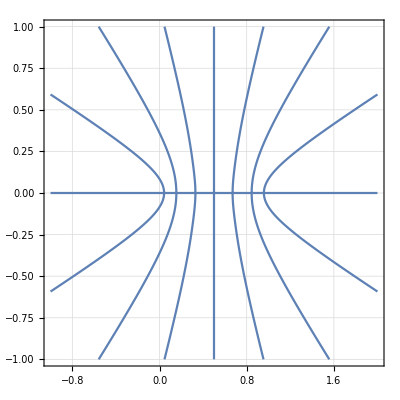

```mathematica
imμ =im/.μ-> 3.8284;
ContourPlot[imμ== 0,{x,-1,2},{y,-1,1},GridLines->Automatic, MaxRecursion->5]
```

```mathematica
rlist={};
Do[AppendTo[rlist, FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦i,1,2⟧/.{y-> ys⟦i,1,2⟧}/.x-> x0 ]/.μ-> 3.8284],{i,2,7}];
```

```mathematica
ϵlist = {};
Do[AppendTo[ϵlist, Reduce[Abs[rlist⟦i⟧]== 1,ϵ,Reals]],{i,1,6}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

Part::partw: Part 5 of x0==0.369183 does not exist.

ParametricPlot::plln: Limiting value 1.00001 x0 in {x0,d,u} is not a machine-sized real number.

Part::partw: Part 5 of x0==0.369183 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 1.00001 x0 in {x0,d,u} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

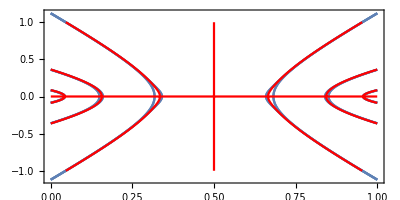

```mathematica
ranges = {{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,4,5,6,7,8,9,10},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}};
dp = 0;
up  = 1;
pplots={};
Do[i= n-1;
Do[ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦i,j⟧;
Which[j ==ranges⟦i,1⟧,d=0;u=0.9999ϵlist⟦i,j,1,2⟧,
j>ranges⟦i,1⟧ && j<ranges⟦i,-1⟧, d= 1.00001ϵlist⟦i,j,1,1⟧;u = 0.999999ϵlist⟦i,j,1,5⟧,
j == ranges⟦i,-1⟧, d=1.00001ϵlist⟦i,j,1,2⟧; u=1];
part1 = ϵlist⟦i,j,2,1,2⟧;
part2 = ϵlist⟦i,j,2,2,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part1, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part1, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0+part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]],
{j,ranges⟦i⟧}],
{n,{2,3,4,5,6,7}}];
img = Show[pplots,ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic,ContourStyle->Red, MaxRecursion->5],PlotRange-> Automatic, AspectRatio-> 1/2]
```

```mathematica
maxvalues = {0.043638217953774955,0.1597920544491029,0.3388};
minvalues = {0.04060225362270445,0.14913012884644786,0.3186};
```

```mathematica
partA = ϵlist⟦1,1,2,1,2⟧;
listamax = Table[{x0-partA,  ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.0000001,maxvalues⟦2⟧,0.00001}];
AppendTo[listamax,{maxvalues⟦2⟧,0}];
f2max = Interpolation[listamax, InterpolationOrder->2, Method->"Hermite"];
f2min = Interpolation[Table[{x0+partA,  ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.000000000001,minvalues⟦2⟧,0.00001}]];
```

```mathematica
partA = ϵlist⟦3,1,2,1,2⟧;
listamax = Table[{x0-partA,  ys⟦5,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.000000000001,maxvalues⟦1⟧,0.00001}];
AppendTo[listamax,{maxvalues⟦1⟧,0}];
f1max = Interpolation[listamax];
f1min = Interpolation[Table[{x0+partA,  ys⟦5,1,2⟧/.{μ-> 3.8284,x-> x0} },{x0,0.0000000001,minvalues⟦1⟧,0.00001}]];
```

```mathematica
ranges = {{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,5,6,8,9,10},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}};
dp = 0;
up  = 1;
pplotsmin={};
pplotsmax={};
Do[i= n-1;
Do[ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦i,j⟧;
Which[j ==ranges⟦i,1⟧,d=0;u=0.999999999999ϵlist⟦i,j,1,2⟧,
j>ranges⟦i,1⟧ && j<ranges⟦i,-1⟧, d= 1.00000000001ϵlist⟦i,j,1,1⟧;u = 0.999999999999ϵlist⟦i,j,1,5⟧,
j == ranges⟦i,-1⟧, d=1.00000000001ϵlist⟦i,j,1,2⟧; u=1];
part1 = ϵlist⟦i,j,2,1,2⟧;
part2 = ϵlist⟦i,j,2,2,2⟧;
AppendTo[pplotsmin,Table[{x0+part1, ysn},{x0,d,u,0.0001}]];
AppendTo[pplotsmax,Table[{x0-part1, ysn},{x0,d,u,0.0001}]],
{j,ranges⟦i⟧}],
{n,{7}}];
```

```mathematica
pplots2min = Flatten[pplotsmin,1];
idelmin={};
For[i=0,i<Length[pplots2min],i++;
If[(Im[pplots2min⟦i,2⟧]≠ 0),AppendTo[idelmin,{i}],None];
If[pplots2min⟦i,1⟧> 0.5, AppendTo[idelmin,{i}],None]]

pplots2max = Flatten[pplotsmax,1];
idelmax={};
For[i=0,i<Length[pplots2max],i++;
If[(Im[pplots2max⟦i,2⟧]≠ 0),AppendTo[idelmax,{i}],None];
If[pplots2max⟦i,1⟧> 0.5, AppendTo[idelmax,{i}],None]]

listamax = Delete[pplots2max, idelmax];
AppendTo[listamax,{maxvalues⟦3⟧,0}];

f3max= Interpolation[listamax,Method->"Spline",InterpolationOrder->2];
f3min= Interpolation[Delete[pplots2min, idelmin],Method->"Hermite",InterpolationOrder->2];
```

Greater::nord: Invalid comparison with 0.325868-2.20404×10^-6 ⅈ attempted.

Greater::nord: Invalid comparison with 0.412929+2.20404×10^-6 ⅈ attempted.

```mathematica
band1pts = {};
up =maxvalues⟦1⟧;
For[i=0,i<10000,i++;
px= RandomReal[{minvalues⟦1⟧,up}];
If[px<minvalues⟦1⟧,pmax = Re[f1max[px]];pmin = Re[f1min[px]], 
pmax=Re[f1max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band1pts,{px,a py}]];
```

```mathematica
band2pts = {};
up =maxvalues⟦2⟧;
For[i=0,i<10000,i++;
px= RandomReal[{minvalues⟦2⟧,up}];
If[px<minvalues⟦2⟧,pmax = Re[f2max[px]];pmin = Re[f2min[px]], 
pmax=Re[f2max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band2pts,{px,a py}]];
```

```mathematica
band3pts = {};
up =maxvalues⟦3⟧;
For[i=0,i<10000,i++;
px= RandomReal[{minvalues⟦3⟧,up}];
If[px<minvalues⟦3⟧,pmax = Re[f3max[px]];pmin = Re[f3min[px]], 
pmax=Re[f3max[px]];pmin=0];
py = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band3pts,{px,a py}]];
```

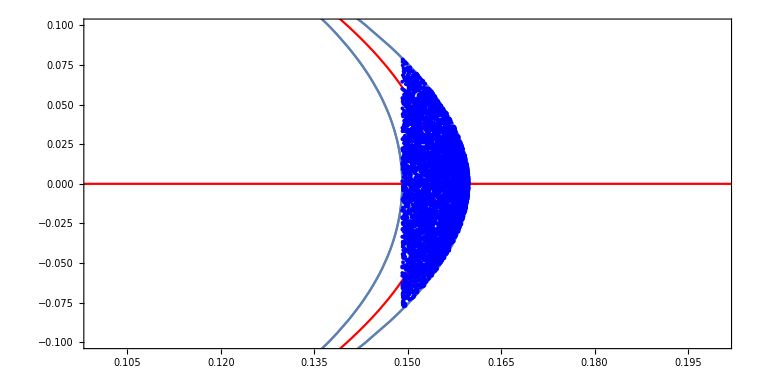

```mathematica
Show[img,ListPlot[band2pts, PlotStyle->Blue],ListPlot[band1pts, PlotStyle->Yellow], ListPlot[band3pts, PlotStyle->Red], PlotRange-> {{0.1,0.2},{-0.1,0.1}}]
```

Mapeamento dos pontos por banda - Tracking do map1 sem imposição de escopo [-∞, +∞]

```mathematica
μ=3.8284;
  statsb1={};
For[i=0,i< Length[band1pts],i++;
x = band1pts⟦i,1⟧;
y = band1pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[statsb1,{x,y}]]

μ=3.8284;
  statsb2={};
For[i=0,i< Length[band2pts],i++;
x = band2pts⟦i,1⟧;
y = band2pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[statsb2,{x,y}]]

μ=3.8284;
  statsb3={};
For[i=0,i< Length[band3pts],i++;
x = band3pts⟦i,1⟧;
y = band3pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[statsb3,{x,y}]]
```

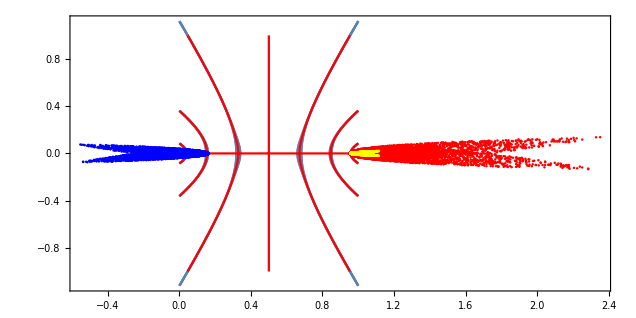

```mathematica
Show[img,ListPlot[statsb2, PlotStyle->Blue], ListPlot[statsb3, PlotStyle->Red],ListPlot[statsb1, PlotStyle->Yellow]]
```

Mapeamento dos pontos por banda - Tracking do map1 com imposição de escopo [0, 1]

```mathematica
stats2b1 ={};
points1 = {};
Do[xp = statsb1⟦j,1⟧;
yp =  statsb1⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points1,{xp,yp}],{j,1,Length[statsb1]}] 
stats2b1 = Partition[points1,Length[statsb1]];

stats2b2 ={};
points2 = {};
Do[xp = statsb2⟦j,1⟧;
yp =  statsb2⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points2,{xp,yp}],{j,1,Length[statsb2]}] 
stats2b2 = Partition[points2,Length[statsb2]];

stats2b3 ={};
points3= {};
Do[xp = statsb3⟦j,1⟧;
yp =  statsb3⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points3,{xp,yp}],{j,1,Length[statsb3]}] 
stats2b3 = Partition[points3,Length[statsb3]];
```

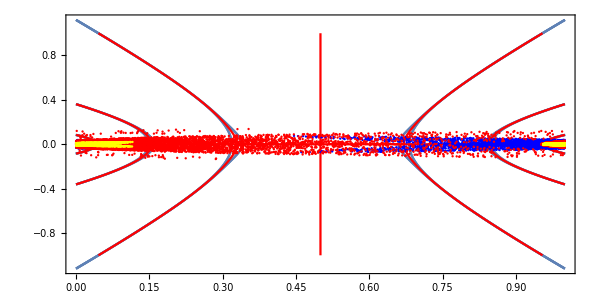

```mathematica
Show[img,ListPlot[stats2b2, PlotStyle->Blue], ListPlot[stats2b3, PlotStyle->Red],ListPlot[stats2b1, PlotStyle->Yellow]]
```

Mapeamento dos pontos por banda - Tracking do map3 sem imposição de escopo

```mathematica
μ=3.8284;
  stats3b1={};
For[i=0,i< Length[band1pts],i++;
x = band1pts⟦i,1⟧;
y = band1pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map3[x,y,μ]],Im[map3[x,y,μ]]}];
AppendTo[stats3b1,{x,y}]]

μ=3.8284;
  stats3b2={};
For[i=0,i< Length[band2pts],i++;
x = band2pts⟦i,1⟧;
y = band2pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map3[x,y,μ]],Im[map3[x,y,μ]]}];
AppendTo[stats3b2,{x,y}]]

μ=3.8284;
  stats3b3={};
For[i=0,i< Length[band3pts],i++;
x = band3pts⟦i,1⟧;
y = band3pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map3[x,y,μ]],Im[map3[x,y,μ]]}];
AppendTo[stats3b3,{x,y}]]
```

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Orange],PlotRange-> {{0,1},{-0.01,0.01}}]
```

-Graphics-

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Orange],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Yellow](*, PlotRange-> {{0,1},{-0.01,0.01}}*),PlotRange-> {{0.95,0.97},{-0.001,0.001}}]
```

-Graphics-

Mapeamento dos pontos por banda - Tracking do map3 sem imposição de escopo [0, 1]

```mathematica
stats3b10 ={};
points1 = {};
Do[xp = stats3b1⟦j,1⟧;
yp =  stats3b1⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points1,{xp,yp}],{j,1,Length[stats3b1]}] 
stats3b10 = Partition[points1,Length[stats3b1]];

stats3b20 ={};
points2 = {};
Do[xp = stats3b2⟦j,1⟧;
yp =  stats3b2⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points2,{xp,yp}],{j,1,Length[stats3b2]}] 
stats3b20 = Partition[points2,Length[stats3b2]];

stats3b30 ={};
points3= {};
Do[xp = stats3b3⟦j,1⟧;
yp =  stats3b3⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points3,{xp,yp}],{j,1,Length[stats3b3]}] 
stats3b30 = Partition[points3,Length[stats3b3]];
```

```mathematica
Show[img,ListPlot[stats3b20, PlotStyle->Blue], ListPlot[stats3b30, PlotStyle->Red],ListPlot[stats3b10, PlotStyle->Orange]]
```

-Graphics-

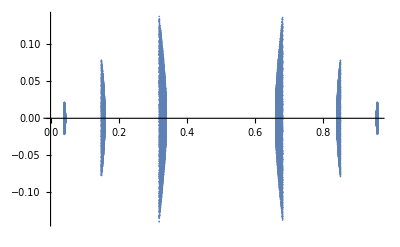

```mathematica
totalbands = Flatten[{band1pts,band2pts,band3pts},1];
ListPlot[totalbands]
```

```mathematica
μ=3.8284;
  stats={};
For[i=0,i< Length[totalbands],i++;
x = totalbands⟦i,1⟧;
y = totalbands⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[stats,{x,y}]]
```

```mathematica
μ=3.8284;
  stats2it={};
For[i=0,i< Length[stats],i++;
x = stats⟦i,1⟧;
y = stats⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[stats2it,{x,y}]]
```

```mathematica
stats2 ={};
points = {};
Do[xp = stats⟦j,1⟧;
yp =  stats⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points,{xp,yp}],{j,1,Length[stats]}] 
stats2 = Partition[points,Length[stats]];
```

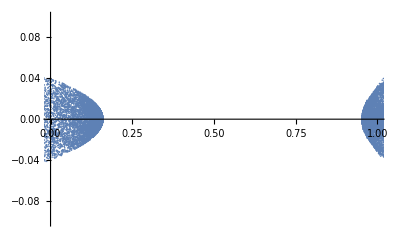

```mathematica
ListPlot[stats,PlotRange->{{0,1},{-0.1,0.1}}]
```

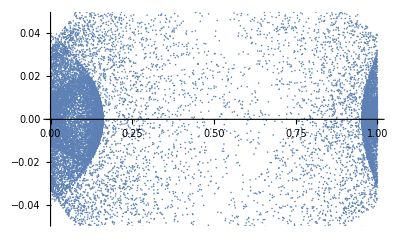

{{0.958785,0.00183676},{0.923869,-0.000965257},{0.958187,0.000512149},{0.922867,0.00736069},{-1.02356,-1.16701},{-1.27081,-1.17905},12988,{0.954479,0.0359353},{-12.7335,10.652},{0.957629,-0.00325414},{-186.329,-92.7483},{-1149.73,419.984},{0.245148,0.540326}}
 |  |  |  |

```mathematica
ListPlot[stats2]
```

```mathematica
step = 0.005;
```

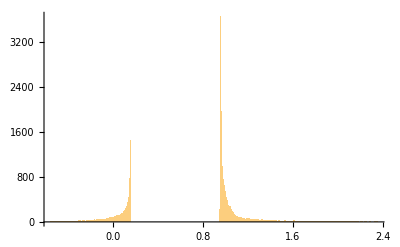

```mathematica
Show[Histogram[stats⟦All,1⟧, {step}]]
```

```mathematica
stats
```

{{1.02577,0.0128977},{0.995098,-0.00697509},{1.01821,0.00489234},{0.959466,-0.00223588},{0.963115,0.00130416},{0.999136,0.000389567},12988,{0.962028,-0.00265214},{1.20462,-0.0128191},{1.0831,-0.0506258},{0.965508,0.00158665},{0.956474,0.000726878},{1.0135,0.0109635}}
 |  |  |  |

```mathematica
BinCounts[stats⟦All,1⟧,{0,1,step}]
```

{78,85,93,87,92,71,98,113,98,112,101,107,93,133,137,125,143,149,163,183,198,193,235,226,266,276,350,388,440,539,781,1453,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,226,3654,1966,1349,981,870,750,641,557,542}

Será que é possível encontrar uma relação step x blur?

```mathematica
prepairpeaks =FindPeaks[BinCounts[stats⟦All,1⟧,{0,1,step}],1.7];
pairpeaks =step prepairpeaks⟦All,1⟧
```

{0.16,0.96}

```mathematica
stats⟦All,1⟧
```

{0.959017,0.967361,0.958317,0.967552,1.01632,1.01857,1.00382,0.956613,0.96332,0.999832,0.959739,1.00188,0.980919,0.995436,12972,1.07474,1.14824,1.2814,0.991158,1.09477,1.04453,0.964063,0.958091,0.965453,1.07608,0.955842,1.20121,1.33057,0.997657}
 |  |  |  |

```mathematica
1.7/0.005
```

340.

Variação do pico com μ. 
- Qual o ponto de partida?